```mathematica
SetDirectory[NotebookDirectory[]];
```

We define the following parameters:
a = v/(2 α)
b = (m_χ α)/m_ϕ
β  = 2 (m_ϕ α)/(m_χ v^2)= 1/(2 a^2 b)
The classical regime is valid when 2 ab >> 1

## Constants

```mathematica
kmsToc = 1/(2.995 10^5);
GeVtoInvcm = 5.05  10^13;
cmtoInvGeV =  1/GeVtoInvcm;
GeVtogram = 1.78 10^-24;
```

```mathematica
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)]
```

## δ_l in various approximations

Assuming it is possible to expand the integrand in Eq. (2) in U, we get the following expressions for the phase-shift and the derivative of the phase-shift:

```mathematica
δlab[a_,b_, l_]:= BesselK[0,l/(b a)]/(2 a);
```

```mathematica
δlparam[mχ_, mϕ_, v_, α_, l_]:=(α BesselK[0,2 l mϕ/(mχ v)])/v;
dδldlab[a_,b_,l_]:=-BesselK[1,l/(a b)]/(2 a^2 b);
```

```mathematica
dδldlparam[mchi_,mphi_,alphaX_,v_,l_]:=-BesselK[1,(l 2 mphi)/(v mchi)](2 alphaX mphi)/(mchi v^2);
```

The full numerical solution for the derivative of the phase-shift (Eq. 21). 
Assuming r0 is the root of k^2-l^2/r^2-2mU=0

```mathematica
r0numerical[mchi_,mphi_,alphaX_,v_,l_]:= r/.FindRoot[((mchi v)^2/4 - (l)^2/r^2 - 2 mchi (-alphaX ⅇ^(-mphi r)/r))^(1/2)==0,{r,2/(mchi v)}];(*This is numerically unstable at the moment*)
```

```mathematica
dδldlFullparam[mchi_,mphi_,alphaX_,v_,l_]:= NIntegrate[-l/(r^2 √((mchi v/2)^2+(2 mchi alphaX ⅇ^(-mphi r))/r - l^2/r^2)) ,{r,r0numerical[mchi,mphi,alphaX,v,l],∞}]+π/2 ;
```

Assuming r0 = l/k

```mathematica
dδldlFullparamSimple[mchi_?NumericQ,mphi_?NumericQ,alphaX_?NumericQ,v_?NumericQ,l_?NumericQ]:= -NIntegrate[1/(r √((r/l mchi v/2)^2+(2 mchi alphaX ⅇ^(-mphi r)r)/l^2 - 1)) ,{r,2 l/(mchi v),∞}]+π/2 ;
```

```mathematica
Clear[dδldlFullparamSimple]
```

## Cross-sections and lmin

```mathematica
lminsmallbeta[a_,b_]:=1/(2a);
lminlargebeta[a_,b_]:= 1/2 a b ProductLog[π/(4 a^4 b^2)] ;
lminNumerical[a_,b_]:= l/.NSolve[1/(2 a^2 b)BesselK[1,l/(a b)]==1,{l}];
```

Using Eqs (18) and (20)  ((σ_T k^2)/(4π)) :

```mathematica
σTkabPatched[a_,b_]:=Piecewise[{{(a^2 b^2)/(2(2 a^2 b)^4)((2 a^2 b)^2-BesselK[1,1/(2 a^2 b)]^2+BesselK[0,1/(2 a^2 b)]BesselK[2,1/(2 a^2 b)]), 1/(2 a^2 b)≤1},{(b^2 a^2)/4 1/2 1/((2 a^2 b)^2)( ProductLog[π/(4 a^4 b^2)])^2((2 a^2 b)^2-BesselK[1, 1/2 ProductLog[π/(4 a^4 b^2)]]^2+BesselK[0, 1/2 ProductLog[π/(4 a^4 b^2)]]BesselK[2,1/2 ProductLog[π/(4 a^4 b^2)]]),1/(2 a^2 b)>1}}];
```

Using Eqs (18) and (20)  (σ_T m_ϕ^2) :

```mathematica
sAnalyticaltimesmϕ2[beta_]:=Piecewise[{{2 π beta^4(1/beta^2-BesselK[1,beta]^2+BesselK[0,beta]BesselK[2,beta]), beta≤1},{π/2 beta^2 ProductLog[π beta^2]^2(1/beta^2-BesselK[1,ProductLog[π beta^2]/2]^2+BesselK[0,ProductLog[π beta^2]/2]BesselK[2,ProductLog[π beta^2]/2]), beta>1}}];
```

```mathematica
-
```

(σ_T m_ϕ^2)  determining lmin numerically:

```mathematica
sAnalyticaltimesmϕ2lmin[a_,beta_]:=4π(-beta^2( a beta lminNumerical[a, 1/(2 a^2 beta)](2 a beta lminNumerical[a, 1/(2 a^2 beta)] BesselK[1,2 a beta lminNumerical[a, 1/(2 a^2 beta)]]^2-2 a beta lminNumerical[a, 1/(2 a^2 beta)] BesselK[0,2 a beta lminNumerical[a, 1/(2 a^2 beta)]]^2 - 2 BesselK[0,2 a beta lminNumerical[a, 1/(2 a^2 beta)]]BesselK[1,2 a beta lminNumerical[a, 1/(2 a^2 beta)]]))+ 1/2(2 a beta lminNumerical[a, 1/(2 a^2 beta)])^2); (*This looks messy but is also just a function of beta*)
```

Calculating the phase-shift numerically:

```mathematica
σNumericalδltimesmϕ2[mchi_?NumericQ,mphi_?NumericQ,alphaX_?NumericQ,v_?NumericQ]:=4 mphi^2(π 4)/(mchi^2 v^2)NIntegrate[(l)Sin[dδldlFullparamSimple[mchi,mphi,alphaX,v,l]]^2,{l,1,1000},WorkingPrecision->15,MaxRecursion->15];
```

Classical Limit from Tulin et. al. ((σ_T k^2)/(4π))

```mathematica
βab[a_,b_]:=1/(2 a^2 b);
σTkTulin[a_,b_]:=(a^2 b^2)/(4π)Piecewise[{{4 Pi βab[a,b]^2 Log[1 + βab[a,b]^(-1)],βab[a,b] < 10^(-1)},{8 Pi βab[a,b]^(2)/(1 + 1.5 βab[a,b]^1.65),10^(-1) ≤ βab[a,b] ≤ 10^3},{ Pi (1 + Log[βab[a,b]] - 1/(2 Log[βab[a,b]]))^2,βab[a,b]>10^3}}];
```

Classical Limit from Tulin et al. (σ_T m_ϕ^2):

```mathematica
sTulintimesmϕ2[beta_] := Piecewise[{{4 Pi beta^2 Log[1 + beta^(-1)],beta< 10^(-1)},{8 Pi beta^(2)/(1 + 1.5 beta^1.65),10^(-1) ≤ beta ≤ 10^3},{ Pi (1 + Log[beta] - 1/(2 Log[beta]))^2,beta>10^3}}];
```

## Plots

Comparison of the integrand in various approximations for different values of β

```mathematica
betalist = logspace[0,3,4];
ablist = Table[{a,b}/.Solve[{1/(2 a^2 b)==beta, 2 a b ==10},{a,b}][[1]],{beta, betalist}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{0.1,50.},{0.01,500.},{0.001,5000.},{0.0001,50000.}}

Parameters that map onto these a,b by fixing alpha = mphi = 0.1
Using 2 ab = 10 and β = 1/(2 a^2 b)
mχ = 50 β;  v = 0.02/β

```mathematica
α = 0.1
mϕ = 0.1
```

Comparison of the integrand in various approximations for different values of β

```mathematica
p1 = LogLogPlot[{l( dδldlab[0.1,50,l])^2, l Sin[dδldlab[0.1,50,l]]^2,l(dδldlFullparamSimple[50 ,0.1,0.1,0.02,l])^2},{l,1,500},PlotLegends->{"l (dδ_l/dl)^2", "l Sin^2(dδ_l/dl)","l (dδ_l/dl)^2 (calculated numerically)"},AxesLabel->{"l","Integrand"},PlotLabel->"β = 1"];
p2 = LogLogPlot[{l( dδldlab[0.01,500,l])^2, l Sin[dδldlab[0.01,500,l]]^2,l(dδldlFullparamSimple[50 10 ,0.1,0.1,0.002,l])^2},{l,1,500},PlotLegends->{"l (dδ_l/dl)^2", "l Sin^2(dδ_l/dl)","l (dδ_l/dl)^2 (calculated numerically)"},AxesLabel->{"l","Integrand"},PlotLabel->"β = 10"];
p3 =  LogLogPlot[{l( dδldlab[0.001,5000,l])^2, l Sin[dδldlab[0.001,5000,l]]^2,l(dδldlFullparamSimple[50 100 ,0.1,0.1,0.0002,l])^2},{l,1,500},PlotLegends->{"l (dδ_l/dl)^2", "l Sin^2(dδ_l/dl)","l (dδ_l/dl)^2 (calculated numerically)"},AxesLabel->{"l","Integrand",PlotLabel->"β = 100"}];
p4 =   LogLogPlot[{l( dδldlab[0.0001,50000,l])^2, l Sin[dδldlab[0.0001,50000,l]]^2,l(dδldlFullparamSimple[50 1000 ,0.1,0.1,0.00002,l])^2},{l,1,500},PlotLegends->{"l (dδ_l/dl)^2", "l Sin^2(dδ_l/dl)","l (dδ_l/dl)^2 (calculated numerically)"},AxesLabel->{"l","Integrand"},PlotLabel->"β = 1000"];
```

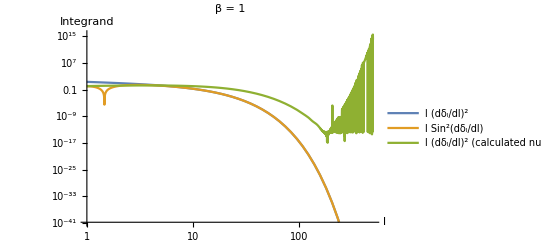

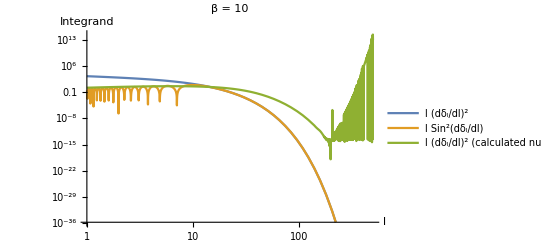

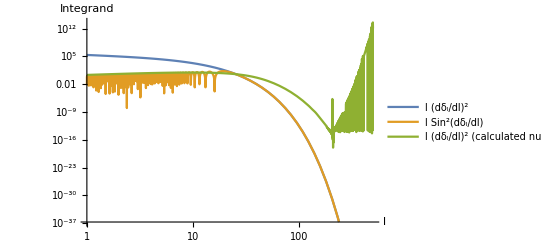

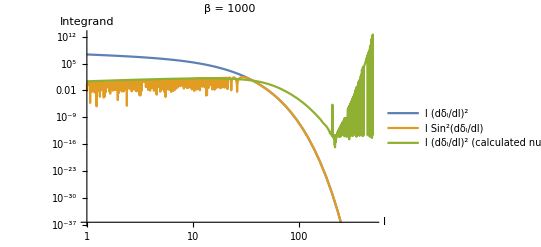

```mathematica
Show[p1]
Show[p2]
Show[p3]
Show[p4]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

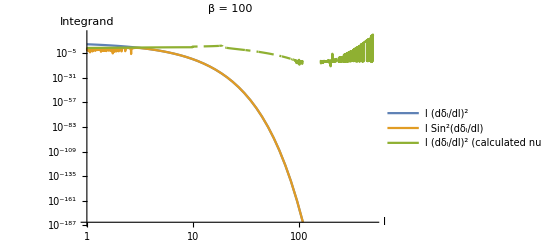

```mathematica
LogLogPlot[{l( dδldlab[0.001,500,l])^2, l Sin[dδldlab[0.001,500,l]]^2,l(dδldlFullparam[500,0.1,0.1,0.002,l])^2},{l,1,500},PlotLegends->{"l (dδ_l/dl)^2", "l Sin^2(dδ_l/dl)","l (dδ_l/dl)^2 (calculated numerically w/ r0≠ l/k)"},AxesLabel->{"l","Integrand"},PlotLabel->"β = 100"]
```

### (σ_T m_ϕ^2)/π as a function of β comparison between Classical and Analytical Results:

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

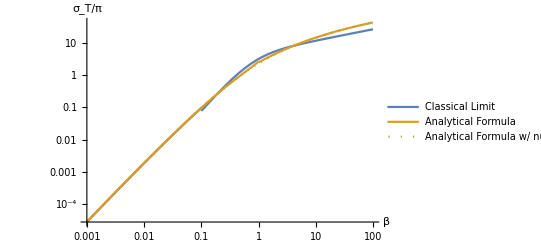

```mathematica
LogLogPlot[{1/π sTulintimesmϕ2[beta],1/π sAnalyticaltimesmϕ2[beta],1/π sAnalyticaltimesmϕ2lmin[0.001,beta]},{beta,0.001,100}, AxesLabel->{"β","σ_T/π"},PlotLegends->{"Classical Limit","Analytical Formula","Analytical Formula w/ numerical lmin"},PlotStyle->{Thick,Thick,Dotted}]
```

### Relative error between anaytic and classical expressions:

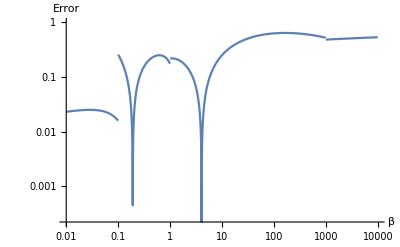

```mathematica
LogLogPlot[{Abs[1/π sAnalyticaltimesmϕ2[beta]-1/π sTulintimesmϕ2[beta]]/(1/π sTulintimesmϕ2[beta])},{beta,0.01,10000}, AxesLabel->{"β","Error"}]
```

### Relative error between the analytic expression for the cross-section and when lmin is calculated numerically

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

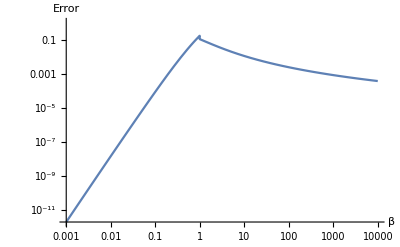

```mathematica
LogLogPlot[{Abs[1/π sAnalyticaltimesmϕ2[beta]-1/π sAnalyticaltimesmϕ2lmin[0.001,beta]]/(1/π sAnalyticaltimesmϕ2lmin[0.001,beta])},{beta,0.001,10000}, AxesLabel->{"β","Error"}]
```

### Cross-section when dδl/dl is calculated numerically

```mathematica
σNumericalδltimesmϕ2List = Table[{beta, 1/π σNumericalδltimesmϕ2[50 beta, 0.1,0.1,0.02/beta]},{beta,logspace[-1,3,40]}];
```

```mathematica
sTulintimesmϕ2List = Table[{beta,1/π sTulintimesmϕ2[beta]},{beta, logspace[-2,3,40]}];
σAnalytictimesmϕ2List = Table[{beta, 1/π sAnalyticaltimesmϕ2[beta]},{beta, logspace[-2,3,40]}];
```

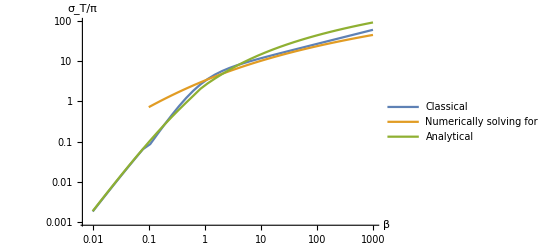

```mathematica
ListLogLogPlot[{sTulintimesmϕ2List,σNumericalδltimesmϕ2List, σAnalytictimesmϕ2List},Joined->True,PlotLegends->{"Classical","Numerically solving for dδ_l/dl","Analytical"},AxesLabel->{"β","σ_T/π"}]
```

## Non-exhaustive list of things that don’t work

(This might be slightly convoluted because I’m copy-pasting from a different messier notebook without clean-up. Sorry!)
Considering an lmax:

```mathematica
lmax[a_,b_]:=l/.FindRoot[-1/(2 a^2 b)BesselK[1, l/(a b)] + 1/l BesselK[0,l/(a b)]==0,{l,0.1}];
σAnBetaTestwithlmax[a_, beta_]:=4π(-beta^2((2/2 a beta lminNumerical[a, 1/(2 a^2 beta)](2 a beta lminNumerical[a, 1/(2 a^2 beta)] BesselK[1,2 a beta lminNumerical[a, 1/(2 a^2 beta)]]^2-2 a beta lminNumerical[a, 1/(2 a^2 beta)] BesselK[0,2 a beta lminNumerical[a, 1/(2 a^2 beta)]]^2 - 2 BesselK[0,2 a beta lminNumerical[a, 1/(2 a^2 beta)]]BesselK[1,2 a beta lminNumerical[a, 1/(2 a^2 beta)]]))-(2/2 a beta lmax[a, 1/(2 a^2 beta)](2 a beta lmax[a, 1/(2 a^2 beta)] BesselK[1,2 a beta lmax[a, 1/(2 a^2 beta)]]^2-2 a beta lmax[a, 1/(2 a^2 beta)] BesselK[0,2 a beta lmax[a, 1/(2 a^2 beta)]]^2 - 2 BesselK[0,2 a beta lmax[a, 1/(2 a^2 beta)]]BesselK[1,2 a beta lmax[a, 1/(2 a^2 beta)]])))+ 1/2(2 a beta lminNumerical[a, 1/(2 a^2 beta)])^2);
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

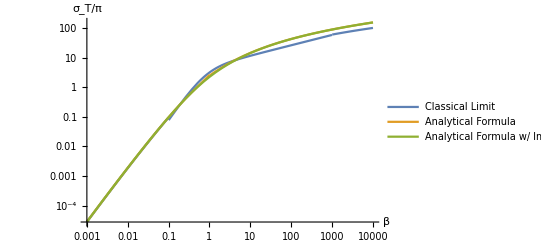

```mathematica
LogLogPlot[{1/π sTulintimesmϕ2[beta],1/π sAnalyticaltimesmϕ2[beta], 1/π σAnBetaTestwithlmax[0.001,beta]},{beta,0.001,10000}, AxesLabel->{"β","σ_T/π"},PlotLegends->{"Classical Limit","Analytical Formula", "Analytical Formula w/ lmax"}]
```